## Definiciones

```mathematica
Get["~/Documents/libs/QMB.wl"]
Get["/home/jadeleon/Documents/chaos_meets_channels/Mathematica_packages/Chaometer.wl"]
```

```mathematica
LogSpace[start_,end_,n_]:=Exp@Subdivide[Log[start],Log[end],n-1]
```

## Datos matrices de Choi

```mathematica
t0=0.1;tf=1000;
```

```mathematica
t=LogSpace[t0,tf,100];
```

```mathematica
L=7;
hx=1.;
```

```mathematica
points = Tuples[{#,#}]&[Subdivide[0., 3., 9]];
lenpoints = Length[points];
```

```mathematica
Do[
{hz,J} = points[[i]];

H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenvals,eigenvecs}=Chop@Eigensystem[H];

x=RandomInteger[100000];SeedRandom[x];
ψ=RandomChainProductState[L-1];
A=KroneckerProduct[IdentityMatrix[2^(L-1),SparseArray]/2,Dyad[ψ]];

P=Transpose[eigenvecs];Pinv=Conjugate[eigenvecs];
ClearAll[U];U[t_]:=P.DiagonalMatrix[Exp[-I*eigenvals*t],TargetStructure->"Sparse"].Pinv;

chois=Table[ChoiMatrix[U[j],A,L],{j,t}];
Export["~/Documents/chaos_meets_channels/ja_files/data/chois/wisniacki/L_7_hx_1_hz_"<>ToString[NumberForm[hz,{Infinity,2}]]<>"_J_"<>ToString[NumberForm[J,{Infinity,2}]]<>"/"<>StringPadLeft[ToString[k],3,"0"]<>".csv",
Prepend[Flatten/@chois,{"Choi matrices from t=0 to t=1000 log spaced, 100 points. Initial state of environment generated with SeedRandom["<>ToString[x]<>"];ψ=RandomChainProductState[L-1];"}],
"CSV"];

,{i,lenpoints},{k,100}]
```

## Pureza de Choi promedio

```mathematica
points = Tuples[{#,#}]&[Subdivide[0., 3., 9]];
lenpoints = Length[points];
```

```mathematica
points
```

{{0.,0.},{0.,0.333333},{0.,0.666667},{0.,1.},{0.,1.33333},{0.,1.66667},{0.,2.},{0.,2.33333},{0.,2.66667},{0.,3.},{0.333333,0.},{0.333333,0.333333},{0.333333,0.666667},{0.333333,1.},{0.333333,1.33333},{0.333333,1.66667},{0.333333,2.},{0.333333,2.33333},{0.333333,2.66667},{0.333333,3.},{0.666667,0.},{0.666667,0.333333},{0.666667,0.666667},{0.666667,1.},{0.666667,1.33333},{0.666667,1.66667},{0.666667,2.},{0.666667,2.33333},{0.666667,2.66667},{0.666667,3.},{1.,0.},{1.,0.333333},{1.,0.666667},{1.,1.},{1.,1.33333},{1.,1.66667},{1.,2.},{1.,2.33333},{1.,2.66667},{1.,3.},{1.33333,0.},{1.33333,0.333333},{1.33333,0.666667},{1.33333,1.},{1.33333,1.33333},{1.33333,1.66667},{1.33333,2.},{1.33333,2.33333},{1.33333,2.66667},{1.33333,3.},{1.66667,0.},{1.66667,0.333333},{1.66667,0.666667},{1.66667,1.},{1.66667,1.33333},{1.66667,1.66667},{1.66667,2.},{1.66667,2.33333},{1.66667,2.66667},{1.66667,3.},{2.,0.},{2.,0.333333},{2.,0.666667},{2.,1.},{2.,1.33333},{2.,1.66667},{2.,2.},{2.,2.33333},{2.,2.66667},{2.,3.},{2.33333,0.},{2.33333,0.333333},{2.33333,0.666667},{2.33333,1.},{2.33333,1.33333},{2.33333,1.66667},{2.33333,2.},{2.33333,2.33333},{2.33333,2.66667},{2.33333,3.},{2.66667,0.},{2.66667,0.333333},{2.66667,0.666667},{2.66667,1.},{2.66667,1.33333},{2.66667,1.66667},{2.66667,2.},{2.66667,2.33333},{2.66667,2.66667},{2.66667,3.},{3.,0.},{3.,0.333333},{3.,0.666667},{3.,1.},{3.,1.33333},{3.,1.66667},{3.,2.},{3.,2.33333},{3.,2.66667},{3.,3.}}

```mathematica
hz=3.;J=1.;
```

```mathematica
chois=Table[ArrayReshape[#,{4,4}]&/@ToExpression[Import["~/Documents/chaos_meets_channels/ja_files/data/chois/wisniacki/L_7_hx_1_hz_"<>ToString[NumberForm[hz,{Infinity,2}]]<>"_J_"<>ToString[NumberForm[J,{Infinity,2}]]<>"/"<>StringPadLeft[ToString[i],3,"0"]<>".csv"]],{i,100}];
```

```mathematica
chois//Dimensions
```

{100,100,4,4}

```mathematica
purities=Chop[Map[Purity[#]&,chois,{2}]];
```

```mathematica
data={};

Do[
{hz,J} = points[[j]];

(* Importar las matrices de Choi *)
chois=Table[ArrayReshape[#,{4,4}]&/@ToExpression[Import["~/Documents/chaos_meets_channels/ja_files/data/chois/wisniacki/L_7_hx_1_hz_"<>ToString[NumberForm[hz,{Infinity,2}]]<>"_J_"<>ToString[NumberForm[J,{Infinity,2}]]<>"/"<>StringPadLeft[ToString[i],3,"0"]<>".csv"][[2;;]]],{i,100}];

(* Calcular la pureza de las matrices de Choi *)
purities=Chop[Map[Purity[#]&,chois,{2}]];

fig=ListLogLinearPlot[Transpose[{t,#}]&/@purities,
PlotRange->{Full,{-0.02,1.02}},
Joined->True,
(*PlotMarkers->{Automatic,7},*)
PlotLabel->Style["Wisniacki, L=7, h_z="<>ToString[NumberForm[hz,{Infinity,2}]]<>", "<>"J="<>ToString[NumberForm[J,{Infinity,2}]]<>",\n100 estados aleatorios producto",Black,FontSize->22],
PlotStyle->Directive[Gray,Thickness[0.001]],
Frame->True,
FrameStyle->Directive[Black,FontSize->22],
FrameLabel->{TraditionalForm[HoldForm[t]],TraditionalForm[Tr[HoldForm[𝒟]^2]]},
Epilog->{Red,Thick,Opacity[0.75],InfiniteLine[{0.1,0.5},{1000,0.5}],Blue,Thick,Opacity[0.75],InfiniteLine[{0.1,0.25},{1000,0.25}]},
ImageSize->500
];

(* Calcular el promedio temporal de la pureza promedio de Choi *)
tmpAvgChoiPurity=Table[
purityInterp = Interpolation[Transpose[{t,i}]]; 
NIntegrate[purityInterp[t],{t,t0,tf}]/tf
,{i,purities}];

AppendTo[data,{hz,J,Mean[tmpAvgChoiPurity],StandardDeviation[tmpAvgChoiPurity]}];

Export["~/Documents/chaos_meets_channels/ja_files/figs_ja/choi/purity_dynamics/wisniacki/L_7_hx_1_hz_"<>ToString[NumberForm[hz,{Infinity,2}]]<>"_J_"<>ToString[NumberForm[J,{Infinity,2}]]<>".pdf",fig,"PDF"];

,{j,lenpoints}]
```

```mathematica
Chop[data[[All,1;;3]]]
```

{{0,0,0.9999},{0,0.333333,0.369357},{0,0.666667,0.407717},{0,1.,0.373784},{0,1.33333,0.387576},{0,1.66667,0.411647},{0,2.,0.421159},{0,2.33333,0.427527},{0,2.66667,0.449116},{0,3.,0.430187},{0.333333,0,0.9999},{0.333333,0.333333,0.284912},{0.333333,0.666667,0.275202},{0.333333,1.,0.271167},{0.333333,1.33333,0.272262},{0.333333,1.66667,0.288456},{0.333333,2.,0.310772},{0.333333,2.33333,0.330778},{0.333333,2.66667,0.358308},{0.333333,3.,0.412857},{0.666667,0,0.9999},{0.666667,0.333333,0.283832},{0.666667,0.666667,0.277368},{0.666667,1.,0.273037},{0.666667,1.33333,0.275645},{0.666667,1.66667,0.278973},{0.666667,2.,0.291877},{0.666667,2.33333,0.311716},{0.666667,2.66667,0.330319},{0.666667,3.,0.377383},{1.,0,0.9999},{1.,0.333333,0.302459},{1.,0.666667,0.289228},{1.,1.,0.284775},{1.,1.33333,0.284406},{1.,1.66667,0.285619},{1.,2.,0.290362},{1.,2.33333,0.30552},{1.,2.66667,0.316217},{1.,3.,0.339522},{1.33333,0,0.9999},{1.33333,0.333333,0.369433},{1.33333,0.666667,0.338851},{1.33333,1.,0.307421},{1.33333,1.33333,0.302441},{1.33333,1.66667,0.304868},{1.33333,2.,0.302259},{1.33333,2.33333,0.307688},{1.33333,2.66667,0.3129},{1.33333,3.,0.32668},{1.66667,0,0.9999},{1.66667,0.333333,0.438057},{1.66667,0.666667,0.407575},{1.66667,1.,0.354258},{1.66667,1.33333,0.323753},{1.66667,1.66667,0.322178},{1.66667,2.,0.321363},{1.66667,2.33333,0.337279},{1.66667,2.66667,0.336625},{1.66667,3.,0.330916},{2.,0,0.9999},{2.,0.333333,0.505855},{2.,0.666667,0.464827},{2.,1.,0.416556},{2.,1.33333,0.375331},{2.,1.66667,0.34836},{2.,2.,0.334888},{2.,2.33333,0.340854},{2.,2.66667,0.357467},{2.,3.,0.379083},{2.33333,0,0.9999},{2.33333,0.333333,0.538389},{2.33333,0.666667,0.519759},{2.33333,1.,0.466894},{2.33333,1.33333,0.428453},{2.33333,1.66667,0.387755},{2.33333,2.,0.364382},{2.33333,2.33333,0.347164},{2.33333,2.66667,0.352412},{2.33333,3.,0.371327},{2.66667,0,0.9999},{2.66667,0.333333,0.544352},{2.66667,0.666667,0.535804},{2.66667,1.,0.513797},{2.66667,1.33333,0.462193},{2.66667,1.66667,0.424364},{2.66667,2.,0.404113},{2.66667,2.33333,0.376018},{2.66667,2.66667,0.357252},{2.66667,3.,0.362115},{3.,0,0.9999},{3.,0.333333,0.554181},{3.,0.666667,0.538066},{3.,1.,0.526429},{3.,1.33333,0.505108},{3.,1.66667,0.461725},{3.,2.,0.429023},{3.,2.33333,0.422345},{3.,2.66667,0.38611},{3.,3.,0.366076}}

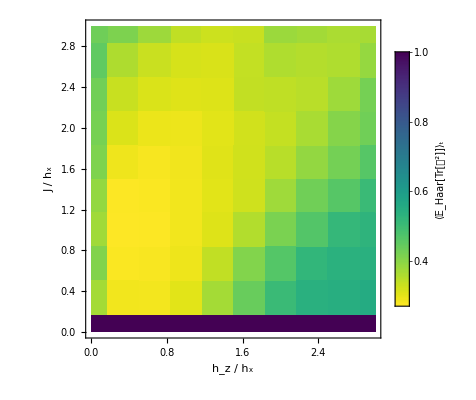

```mathematica
fontSize=18;

fig=ListDensityPlot[Chop[data[[All,1;;3]]],
ColorFunction->(ResourceFunction["ViridisColor"][1-#]&),ColorFunctionScaling->True,
PlotRange->{0.25,1.},
InterpolationOrder->0,
PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"⟨𝔼_Haar[Tr[𝒟^2]]⟩_t",LabelStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black]],Automatic],
Frame->True,
FrameStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black],
FrameLabel->{"h_z / h_x","J / h_x"},
AspectRatio->1
]
```

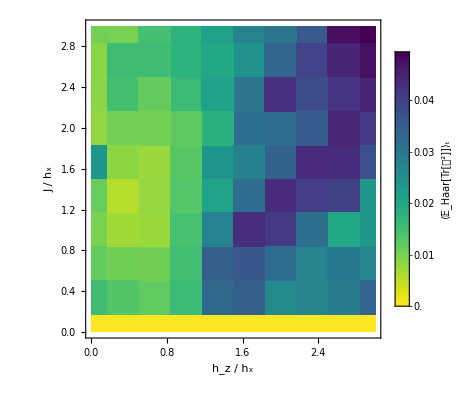

```mathematica
fontSize=18;

fig=ListDensityPlot[Chop[data[[All,{1,2,4}]]],
ColorFunction->(ResourceFunction["ViridisColor"][1-#]&),ColorFunctionScaling->True,
PlotRange->Full,
InterpolationOrder->0,
PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"⟨𝔼_Haar[Tr[𝒟^2]]⟩_t",LabelStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black]],Automatic],
Frame->True,
FrameStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black],
FrameLabel->{"h_z / h_x","J / h_x"},
AspectRatio->1
]
```